# Homework 3: Rabi Oscillations

```mathematica
ClearAll;(* Good idea to always start with this! *)
H = {{V0 , Δ},{Δ, V1}}; (* Diabatic Hamiltonian Matrix *)
H//MatrixForm
```

(V0 | Δ
Δ | V1)

```mathematica
traj= MatrixExp[-I*H*t].{c0,c1}; (* Propagate wavefunction using propagator (NOTE the matrix exponential!) *)
c0t=traj[[1]]; (* Splitting the result for each coefficient *)
c1t=traj[[2]];
```

```mathematica
param={V0->1, V1->2, Δ-> 1}; (* Choose some arbitraty parameters *) 
inicon = {c0->1, c1->0}; (* Initial conditions of starting with only Eigenstate 0*)
```

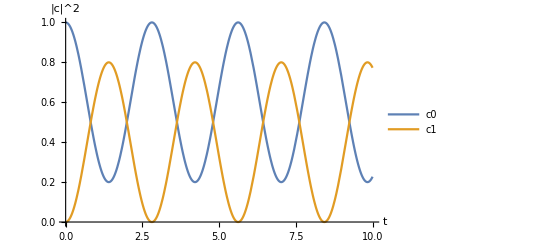

```mathematica
Plot[{Abs[c0t]^2//.param//.inicon,Abs[c1t]^2//.param//.inicon},{t,0,10},AxesLabel->{"t", "|c|^2"},PlotLegends->{"c0","c1"}](* Plotting Absolute square of coefficients as a function of time *)
```

```mathematica
(* For added fun, lets make an interactive plot for which we can change the parameters (Specifically the difference in energy and coupling strenght) *)
```

```mathematica
Manipulate[Plot[{Abs[c0t]^2//.{V0->1, V1->1+ΔV,Δ-> coupling}//.inicon,Abs[c1t]^2//.{V0->1, V1->1+ΔV,Δ-> coupling}//.inicon},{t,0,10},AxesLabel->{"t", "|c|^2"},PlotLegends->{"c0","c1"}], {coupling,0,5},{ΔV,0,5}]
```